```mathematica
Clear["Global`*"];
```

This script analyzes the result of misaligning the Schafter-Kirchhoff fiber collimator by introducing the walkoff with a translation stage from optimal coupling and seeing how the coupled power drops

```mathematica
initialPower = 0.573 (*mW*);
xPosition = {9.745,9.700,9.650,9.600,9.550,9.500,9.450,9.400,9.350,9.300};
coupledPower = {0.413,0.412,0.402,0.375,0.345,0.305,0.264,0.219,0.178,0.137};
```

```mathematica
couplingEfficiency = coupledPower/initialPower
```

{0.720768,0.719023,0.701571,0.65445,0.602094,0.532286,0.460733,0.382199,0.310646,0.239092}

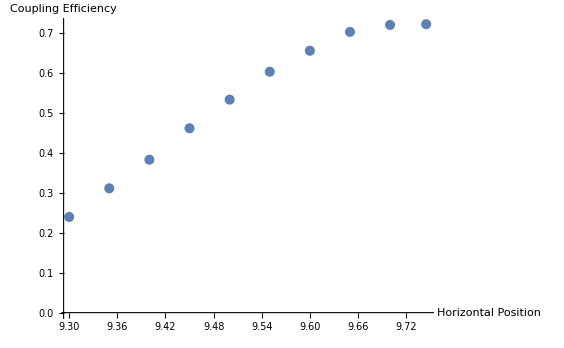

```mathematica
ListPlot[Partition[Riffle[xPosition,couplingEfficiency],2],AxesLabel->{"Horizontal Position","Coupling Efficiency"}]
```

```mathematica
dataToFit = Partition[Riffle[xPosition,couplingEfficiency],2];
```

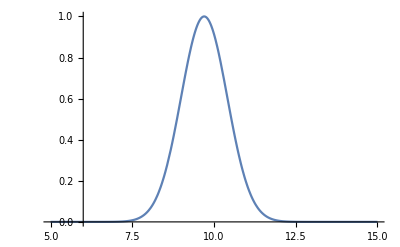

```mathematica
Plot[Exp[(-(x-9.7)^2)/1^2],{x,5,15}]
```

```mathematica
nlm=NonlinearModelFit[dataToFit,Exp[-amp*(x-x0)^2/w^2],{{amp,0.7},{x0,9.745},{w,0.5}},x]
```

FittedModel[ⅇ^(-1.99236 (-«19»+x)^2)]

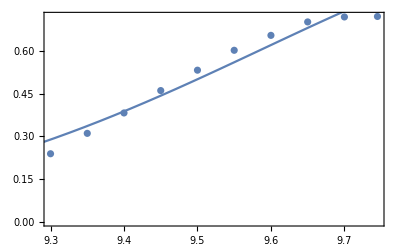

```mathematica
Show[ListPlot[dataToFit],Plot[nlm[x],{x,9,10}],Frame->True]
```

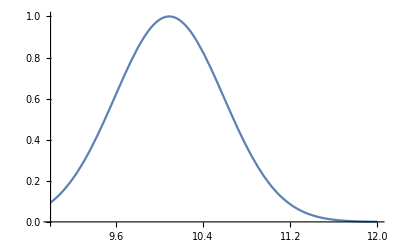

```mathematica
Plot[nlm[x],{x,9,12}]
```